```mathematica
SetDirectory[NotebookDirectory[]];
Nc=3.;
mf2[h_,ρ_]:=(h^2 ρ)/2;
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
F1[q_,ρ_,h_,T_,μ_]:=q^2/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^2/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^2 NIntegrate[(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)Re[F1F1m[q,p0,ps,x,ρ,h,T,μ]]),{q,0.,10.,20.,30.,40.,50.,100.,500.,5000.},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->50,WorkingPrecision->15,AccuracyGoal->10,PrecisionGoal->10];
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((*(2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+*)(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5])(*-(Nc h^2 mf2[h,ρ])/(16 π^2)*);
gammavac2[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->50]);
gamma2[p0_,ps_,ρ_,ρ0_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ]-gammavac2[p0,ps,ρ0,h,Mmass,MZ]+p0^2+ps^2+(λ300 ρ+ν300);
gamma2v1[p0_,ps_,ρ_,ρ0_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ]+p0^2+ps^2+(λ300 ρ+ν300);
λ300=75.8;
ν300=-482.^2;
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

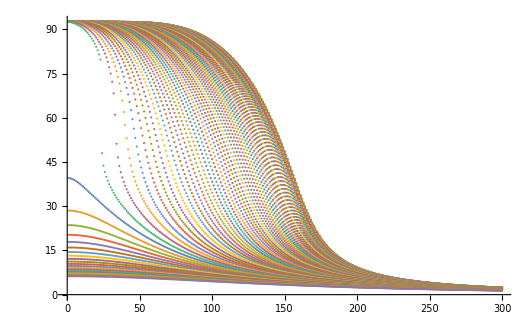

```mathematica
sigmadata=Import["../../sigma0.dat"];
ListPlot[sigmadata]
```

```mathematica
muq=Table[i*5,{i,1,80}];
muq[[56]]
muq[[64]]
sigmadata[[1]][[1]]
```

280

320

92.5785

```mathematica
fixM1=Table[ParallelTable[gamma2[0.,p,(sigmadata[[mu]][[30]])^2/2,(sigmadata[[1]][[1]])^2/2,6.5,30.,mu*5,300,300],{p,1,600,10}],{mu,56,64,1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
ListPlot3D[fixM1]
```

-Graphics3D-

```mathematica
Export["./Ep.dat",Re[fixM1]];
```

```mathematica
(*Epv2mu400T1=ParallelTable[gamma2[0.,p,(sigmadata[[80]][[10]])^2/2,(sigmadata[[1]][[1]])^2/2,6.5,10.,400.,300,300]//Quiet,{p,1,1500,10}];
Epv2mu400T1v1=ParallelTable[gamma2v1[0.,p,(sigmadata[[80]][[10]])^2/2,(sigmadata[[1]][[1]])^2/2,6.5,10.,400.,300,300]//Quiet,{p,1,1500,10}];*)
Epv2mu400T1v2=ParallelTable[gamma2v1[0.,p,(sigmadata[[80]][[10]])^2/2,(sigmadata[[1]][[1]])^2/2,6.5,10.,400.,300,500]//Quiet,{p,1,1500,10}];
```

```mathematica
ps=Table[i,{i,1,1500,10}];
```

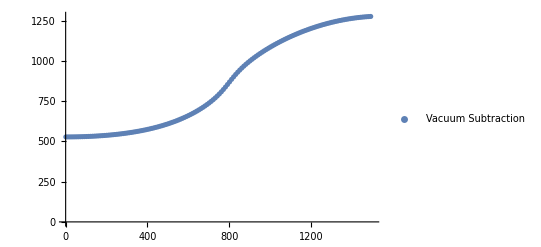

```mathematica
ListPlot[{(*Transpose[{ps,√Epv2mu400T1}],Transpose[{ps,√Epv2mu400T1v1}],*)Transpose[{ps,√Epv2mu400T1v2}]},PlotRange->{{0,1500},All},PlotLegends->{"Vacuum Subtraction","M=300","M=500"}]
```

```mathematica
(*Export["./renormv1.dat",Epv2mu400T1v1];
Export["./renormv2.dat",Epv2mu400T1];*)
Export["./renormM500.dat",Epv2mu400T1v2];
Export["./ps2.dat",ps];
```

```mathematica
Epv2mu400T0=ParallelTable[gamma2[0.,p,(sigmadata[[80]][[1]])^2/2,(sigmadata[[1]][[1]])^2/2,6.5,1.,400.,300,300]//Quiet,{p,1,1500,10}];
Epv2mu400T0v1=ParallelTable[gamma2v1[0.,p,(sigmadata[[80]][[1]])^2/2,(sigmadata[[1]][[1]])^2/2,6.5,1.,400.,300,300]//Quiet,{p,1,1500,10}];
```

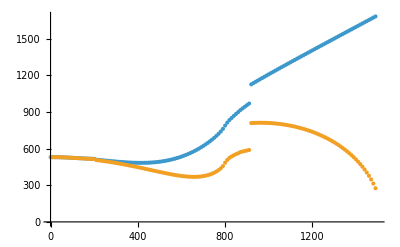

```mathematica
ListPlot[{Transpose[{ps,√Epv2mu400T0}],Transpose[{ps,√Epv2mu400T0v1}]},PlotRange->{{0,1500},All}]
```

```mathematica
vacdata=Table[{p,gammavac[0,p,(sigmadata[[80]][[1]])^2/2,6.5,300,1000]},{p,1,3000,20}];
```

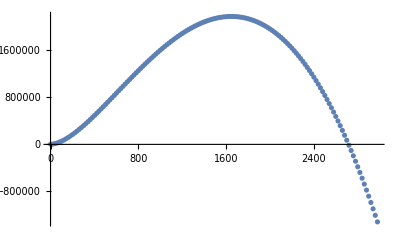

```mathematica
ListPlot[vacdata]
```

```mathematica
thrdata=ParallelTable[{p,gamma2thr[0,p,(sigmadata[[80]][[10]])^2/2,6.5,10.,400.]//Quiet},{p,1,1000,20}];
```

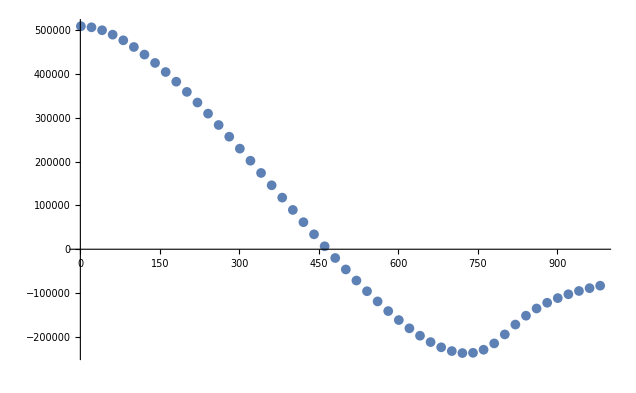

```mathematica
ListPlot[thrdata]
```

```mathematica
vacdata=Table[{p,(*(λ300 (sigmadata[[80]][[10]])^2/2+ν300)+p^2*)-(6.5^2 3)/(8 π^2)((*mf2[6.5,(sigmadata[[80]][[10]])^2/2](2Log[(√mf2[6.5,(sigmadata[[80]][[10]])^2/2])/300])+*)p^2*(-1+Log[(√mf2[6.5,(sigmadata[[80]][[10]])^2/2])/300]+(√(p^2+4 mf2[6.5,(sigmadata[[80]][[10]])^2/2]))/(2 p)(Log[(√(p^2+4mf2[6.5,(sigmadata[[80]][[10]])^2/2])+p)/(√(p^2+4mf2[6.5,(sigmadata[[80]][[10]])^2/2])-p)]))(*1/2 p (-2 p+p Log[mf2[6.5,(sigmadata[[80]][[10]])^2/2]]-2 p Log[300]-√(4 mf2[6.5,(sigmadata[[80]][[10]])^2/2]+p^2) Log[1-p/(√(4 mf2[6.5,(sigmadata[[80]][[10]])^2/2]+p^2))]+√(4 mf2[6.5,(sigmadata[[80]][[10]])^2/2]+p^2) Log[1+p/(√(4 mf2[6.5,(sigmadata[[80]][[10]])^2/2]+p^2))])*))},{p,1,1000,20}];
```

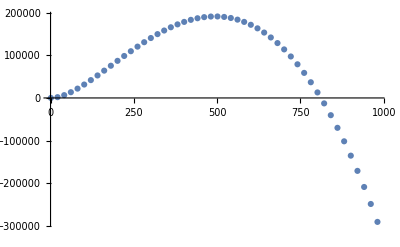

```mathematica
ListPlot[vacdata]
```

```mathematica
vacdatav1=Table[{p,gammavac[0,p,(sigmadata[[80]][[10]])^2/2,6.5,300,300](*+p^2+(λ300 (sigmadata[[80]][[10]])^2/2+ν300)*)},{p,1,1000,20}];
```

```mathematica
ListPlot[vacdatav1]
```

-Graphics-

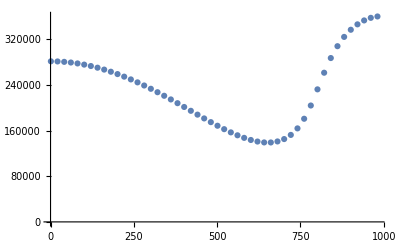

```mathematica
ListPlot[Transpose[{Transpose[vacdatav1][[1]],Transpose[vacdatav1][[2]]+Transpose[thrdata][[2]]}]]
```